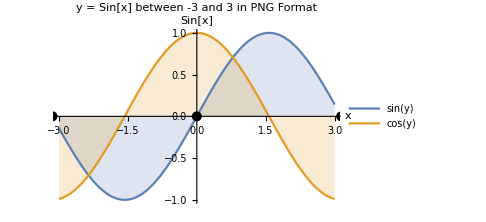

```mathematica
ClearAll[api,format]
api[fwt_String]:= APIFunction[
{
"a"->"Integer",
"b"->"Integer"
},
Function[
Framed@Plot[{Sin[y],Cos[y]},{y,#a,#b},
PlotLabel->Style[Framed["y = Sin[x] between " <> ToString[#a] <> " and " <> ToString[#b] <> " in " <> fwt <> " Format"],12, Black, Background->Lighter[LightGreen]],
Filling->Axis,
AxesLabel->{"x","Sin[x]"},
AxesStyle->{Directive[Thin,Dashed,Black],Black},
PlotLegends->"Expressions",
Epilog->{PointSize[0.02],Point[{-Pi,0}],Point[{0,0}],Point[{Pi,0}],Point[{2*Pi,0}]},
ImageSize->Medium]
],
fwt];
format = "PNG";
api[format][<|"a"->-3,"b"->3|>]
```

```mathematica
ClearAll[cd]
cd[fmt_String]:=CloudDeploy[
api[fmt],
"/coursework/sin-" <> ToLowerCase[fmt] <> "/",
Permissions->"Public"
];
formats = {"PNG","JPG","GIF","SVG"};
Table[cd[f],{f,formats}]
```

{CloudObject[https://www.wolframcloud.com/obj/85100044/coursework/sin-png],CloudObject[https://www.wolframcloud.com/obj/85100044/coursework/sin-jpg],CloudObject[https://www.wolframcloud.com/obj/85100044/coursework/sin-gif],CloudObject[https://www.wolframcloud.com/obj/85100044/coursework/sin-svg]}

```mathematica
ClearAll[url,session]
url= URLBuild[cd[format],<|"a"->-3,"b"->3|>]
session = StartWebSession["Chrome"];
WebExecute[session,{"OpenPage"->url}];
```

https://www.wolframcloud.com/obj/85100044/coursework/sin-png?a=-3&b=3